## 250415 (Pt, inside farady box) _001

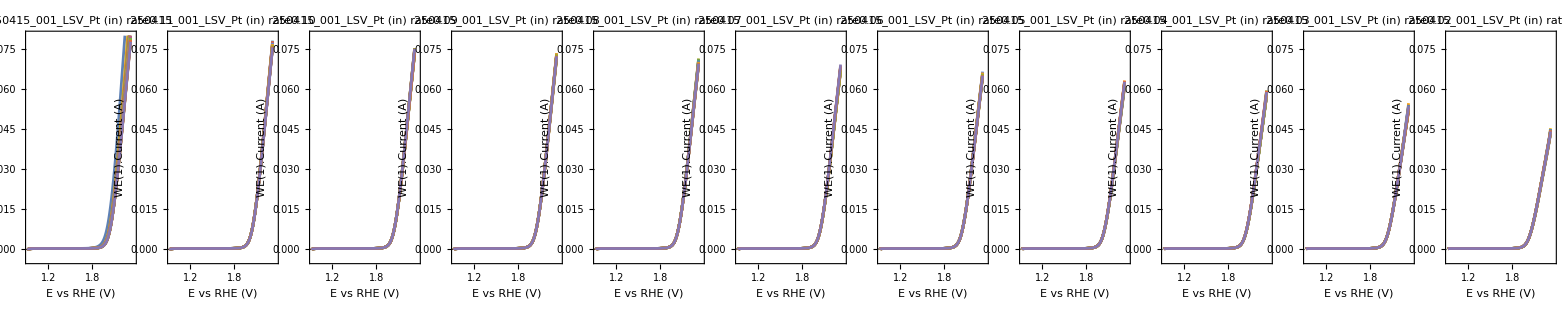

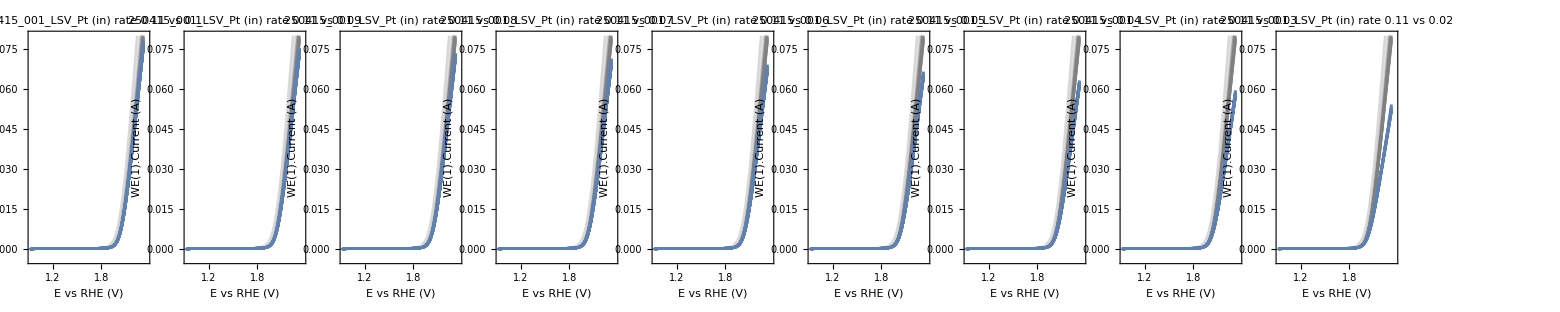

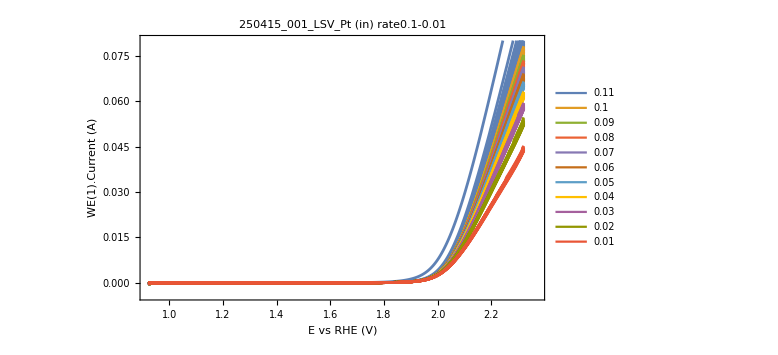

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250415_001_LSV_Pt";
rateList=Range[0.11,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
(*將每個 folder 中的 1–20 號檔案轉為資料矩陣*)
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->4,"FieldSeparators"->"\t"]&/@files;
(*確保每筆資料為二維 {x,y} 格式*)
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];

(*設定轉換用參數*)
pH=13.871;
E0HgHgO=0.0983; (*標準電位*)
conversionShift=0.0592*pH+E0HgHgO; 

(*對每組資料的 x 軸做平移*)
rateDataSetsRHE=rateDataSets/. {x_,y_}:>{x+conversionShift,y};

(*產生圖，每個 rate 一張圖*)
plots=Table[ListLinePlot[rateDataSetsRHE[[i]],PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (in) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*比較 baseline vs 每一個其他 rate，每個圖 20 條+20 條線，共 40 條*)
baselineData=rateDataSetsRHE[[1]]; (*提取rate0.11 當 baseline*)
baselineColor=Directive[Gray,Opacity[0.3]];
comparisonPlots=Table[Module[{testData=rateDataSetsRHE[[i]]},If[Length[testData]==20,ListLinePlot[Join[Table[Style[baselineData[[j]],baselineColor],{j,1,20}],Table[Style[testData[[j]],colors[[1]]],{j,1,20}]],PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (in) rate 0.11 vs "<>ToString[rateList[[i]]],ImageSize->300],Style["Data missing for rate "<>ToString[rateList[[i]]],Red]]],{i,2,Length[rateList]}];
TableForm[{comparisonPlots}]


(*合併所有曲線資料成一個 list，同時建立對應顏色表*)
allCurves=Flatten[rateDataSetsRHE,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->FileNameTake[baseDir,-1]<>" (in) rate0.1-0.01",ImageSize->Large]
```

## 250415 (Pt, outside farady box) _002

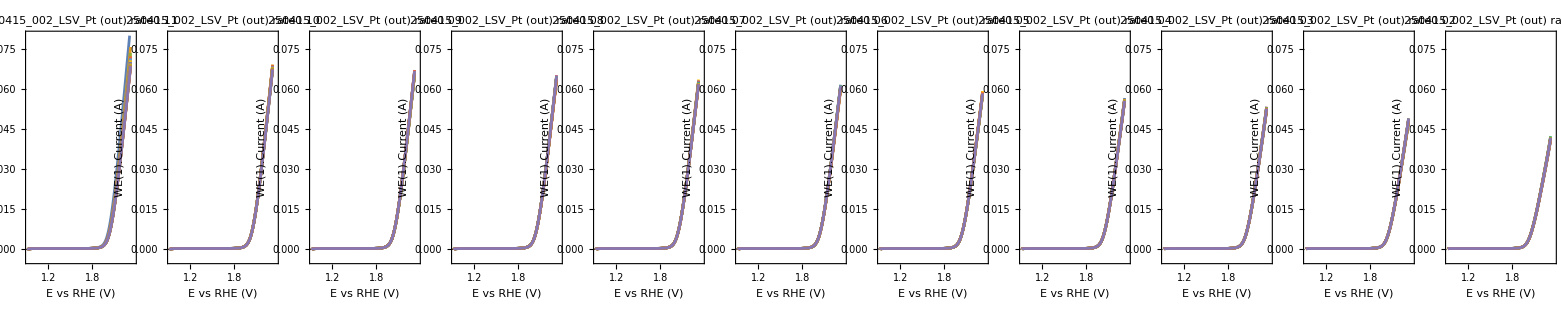

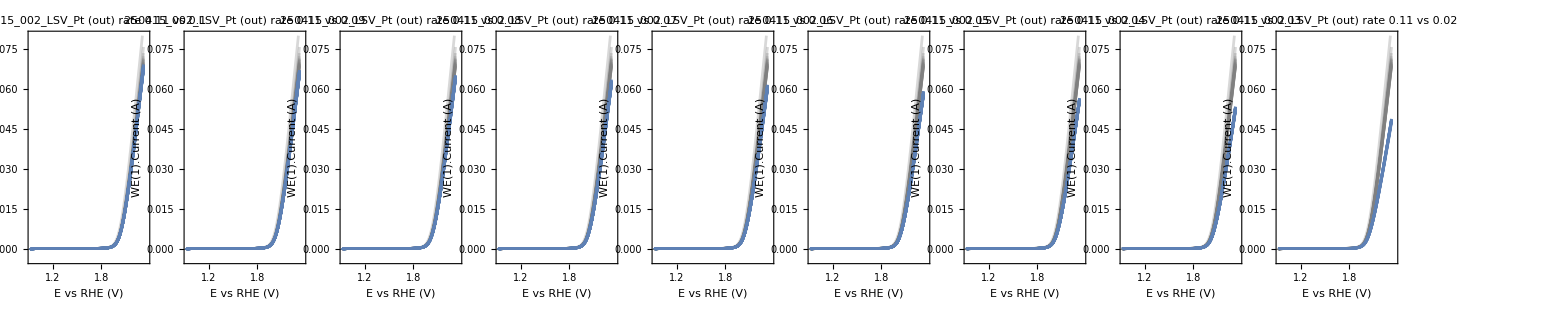

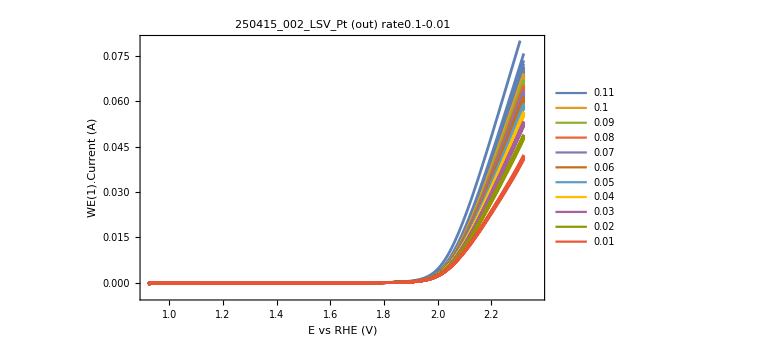

```mathematica
baseDir="C:\\Users\\kelvi\\OneDrive\\桌面\\Data\\250415_002_LSV_Pt";
rateList=Range[0.11,0.01,-0.01];
rateFolders=FileNameJoin[{baseDir,"rate"<>ToString[NumberForm[#,{3,2}]]}]&/@rateList;
rateDataSets=Table[Module[{files,data},files=FileNameJoin[{folder,ToString[#]}]&/@Range[1,20];
data=Import[#,"Table","HeaderLines"->4,"FieldSeparators"->"\t"]&/@files;
data=Module[{d=#},If[MatrixQ[d]&&Depth[d]==3,d,Transpose[d]]]&/@data;
data],{folder,rateFolders}];

(*設定轉換用參數*)
pH=13.871;
E0HgHgO=0.0983; (*標準電位*)
conversionShift=0.0592*pH+E0HgHgO; 

(*對每組資料的 x 軸做平移*)
rateDataSetsRHE=rateDataSets/. {x_,y_}:>{x+conversionShift,y};


plots=Table[ListLinePlot[rateDataSetsRHE[[i]],PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},PlotStyle->ColorData[97,"ColorList"],Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (out) "<>FileNameTake[rateFolders[[i]],-1],ImageSize->300],{i,Length[rateFolders]}];
TableForm[{plots}]

(*比較 baseline(0.01) vs 每一個其他 rate，每個圖 20 條+20 條線，共 40 條*)
baselineData=rateDataSetsRHE[[1]]; 
baselineColor=Directive[Gray,Opacity[0.3]];
comparisonPlots=Table[Module[{testData=rateDataSetsRHE[[i]]},If[Length[testData]==20,ListLinePlot[Join[Table[Style[baselineData[[j]],baselineColor],{j,1,20}],Table[Style[testData[[j]],colors[[1]]],{j,1,20}]],PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLabel->FileNameTake[baseDir,-1]<>" (out) rate 0.11 vs "<>ToString[rateList[[i]]],ImageSize->300],Style["Data missing for rate "<>ToString[rateList[[i]]],Red]]],{i,2,Length[rateList]}];
TableForm[{comparisonPlots}]


allCurves=Flatten[rateDataSetsRHE,1];
colors=ColorData[97,"ColorList"][[1;;Length[rateList]]];
plotColors=Flatten[Table[ConstantArray[colors[[i]],20],{i,Length[rateList]}]];
ListLinePlot[allCurves,PlotRange->{{0+conversionShift,1.45+conversionShift},{-0.004,0.08}},PlotStyle->plotColors,Frame->True,FrameLabel->{"E vs RHE (V)","WE(1).Current (A)"},PlotLegends->Placed[LineLegend[colors,ToString/@rateList],Right],PlotLabel->FileNameTake[baseDir,-1]<>" (out) rate0.1-0.01",ImageSize->Large]
```